## Inverse and Transpose:

```mathematica
(*matrix invertieren und transponieren ist vertauschbar für singuläre matrizen*)
Inverse[Transpose[matrix]]
Transpose[Inverse[matrix]]
```

Inverse[Transpose[matrix]]

Transpose[Inverse[matrix]]

## Rechenregeln mit invertierten Matrizen:

```mathematica
(*um die ausgangsmatrix nach multiplikation mit matrizen wieder zu erhalten muss man das Ergebnis mit den invertierten Matrizen von zuvor in verkeherter Reihenfolge multiplizieren*)
mat1=({{2, 3}, {4, 5}});
mat2=({{3, 4}, {5, 7}});
mat3=({{6, 5}, {4, 1}});
Matrix=({{10, 20}, {30, 40}});

newMat=mat1.mat2.mat3.Matrix
Inverse[mat3].Inverse[mat2].Inverse[mat1].newMat//MatrixForm
```

{{6440,10200},{11340,17960}}

(10 | 20
30 | 40)

```mathematica
Integrate[n^2,n]
```

n^3/3

```mathematica
(*P^-1=P^T*)(*permutationsmatrix: inverse matrix= der transponierten matrix*)
(*P^T*P=I*)(*Identity matrix*)
(*R^T.R is always a symetric matrix when R is rectangular*)
(*(R^T.A)^T=A^T.R^TT=>A^T.R*)(*transpose rule*)
```

```mathematica
RectMatrix={{1,2,3},{2,4,6},{2,6,8},{2,8,10}};
Graphics3D[Table[{Arrow[{{0,0,0},RectMatrix⟦k⟧}],Text[k,RectMatrix⟦k⟧]},{k,1,Length[RectMatrix]}]]
```

-Graphics3D-

{1/4,1/2}

{1-2 x,2 x}

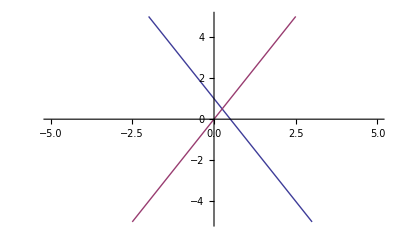

{{x→-1,y→-1}}

```mathematica
lineEquations={y+2x==1,4y+-8x==0};
thePoint=Solve[lineEquations][[1]][[All,2]]

lineFunctions=Flatten[y/.Solve[#,y] & /@lineEquations]

Plot[{lineFunctions[[1]],lineFunctions[[2]]},{x,-10,10},ImageSize->Scaled[1],PlotRange->{{-5,5},{-5,5}}]
Solve[{y-3x==2,y-11x==10}]
```

## Find solution of equation system:

```mathematica
eqns={
5x-3y+3z==10,
14 x-9 y-2 z==40,
4x-12y+4z==30
};
CoordsOfPoint=Solve[eqns][[1]][[All,2]]

funcs=Flatten[z/.(Solve[#,z]&/@eqns)]

SetOptions[Plot3D, ImageSize->Scaled[1],BaseStyle->{FontSize->14}];

Show[Plot3D[{funcs[[1]],funcs[[2]],funcs[[3]]},{x,-40,40},{y,-40,40},PlotRange->{{-40,40},{-40,40},{-140,140}},
AxesLabel->{x,y,z},
PlotStyle->{Blue,Red,Green}],
Graphics3D[{PointSize[.02],RGBColor[1,0,0],Point[CoordsOfPoint]}]]

{1/3 (10-5 x+3 y),1/8 (-20+4 x-3 y),1/2 (15-x+3 y)}
{-45/43,-760/129,-35/43}
```

{95/84,-155/63,-85/84}

{1/3 (10-5 x+3 y),1/2 (-40+14 x-9 y),1/2 (15-2 x+6 y)}

-Graphics3D-

{1/3 (10-5 x+3 y),1/8 (-20+4 x-3 y),1/2 (15-x+3 y)}

{-45/43,-760/129,-35/43}

```mathematica
(*RectMatrix={{1,2,3},{2,4,6},{2,6,8},{2,8,10}};*)
Transpose[RectMatrix].RectMatrix//MatrixForm
RectMatrix.Transpose[RectMatrix]//MatrixForm
```

(13 | 38 | 51
38 | 120 | 158
51 | 158 | 209)

(14 | 28 | 38 | 48
28 | 56 | 76 | 96
38 | 76 | 104 | 132
48 | 96 | 132 | 168)